# Beamshaping Last Updated: 02/08/2022

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## 0 Prep

## 0.0 Setup

### 0.0.1 Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;me=9.10938356*^-31;qe=1.60217662*^-19;c=2.99792458*^8;kb=1.38064852*^-23;
(*derived*)
ke2=2.30707751*^-28;a0=ℏ^2/me/ke2;
```

```mathematica
mm=1*^-3;cm=1.*^-2;um=1.*^-6;
in=2.54*^-2;
```

## 0.1 Matrices

```mathematica
mL[L_]:={{1,L},{0,1}};
mLens[f_]:={{1,0},{-1/f,1}};
```

## 0.2 Functions

```mathematica
Radius[q_]:=#1+#2^2/#1&[Re[q],Im[q]];
```

```mathematica
Waist[q_]:=Sqrt[λ/(-Im[1/q]*π)];
```

```mathematica
NA[q_,f_]:=#1*#2/Sqrt[#1^2*#2^2+1]&[Waist[q],f];
```

```mathematica
Propagate[q_,mat_]:=(q*mat[[1,1]]+mat[[1,2]])/(q*mat[[2,1]]+mat[[2,2]]);
```

## 0.3 q-vectors

```mathematica
q0=z0+ⅈ*b;
```

## 1 TH

```mathematica
λ=3.97*^-7;b=π/λ*(2*^-4)^2;z0=1*in;
```

```mathematica
(**)
```

```mathematica
q1=Propagate[q0,mL[f].mLens[f]]//FullSimplify;(*lens then distance*)
q1
```

(f ((0.+0. ⅈ)+f))/((-0.0254-0.316533 ⅈ)+f)

```mathematica
Waist[q0]
Waist[q1/.{f->5.8*mm}]
NA[q1/.{f->5.8*mm},5.8*mm]
```

200.643

3.6647

0.0212505

```mathematica
(**)
Clear[z0]
```

```mathematica
q0
```

(0.+0.316533 ⅈ)+z0

```mathematica
sc1=Propagate[q0,mL[x](*.mLens[f]*)]//FullSimplify;
sc2=sc1/.{z0->-5*in}//FullSimplify;
```

```mathematica
f1[f_,x_]:=Evaluate[Waist[sc2]]
```

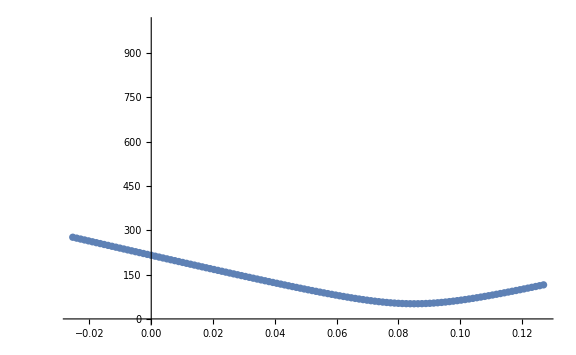

```mathematica
y1=Range[-1*in,5*in,0.05*in];
th1=f1[100*mm,#]&/@y1;
ListPlot[th1,ImageSize->Large,DataRange->{-1*in,5*in},PlotRange->{0,1000}]
```